```mathematica
elementList={"Sc"->1,"Ti"->2,"V"->3,"Cr"->4,"Mn"->5,"Fe"->6,"Co"->7,"Ni"->8,"Cu"->9,"Zn"->10,"Y"->11,"Zr"->12,"Nb"->13,"Mo"->14,"Tc"->15,"Ru"->16,"Rh"->17,"Pd"->18,"Ag"->19,"Hf"->20,"Ta"->21,"W"->22,"Re"->23,"Os"->24,"Ir"->25,"Pt"->26,"Au"->27};
elements=List@@@elementList//Transpose//First;
targets = {ORR -> -1.51, CORedCO -> -1.20, ORedCO -> -1.25};
```

## Parse Data:

```mathematica
data=Import["/home/marco/fridbDemo/allresults.json"];
```

Parse 38 atom NP oxygen binding energy:

```mathematica
atoms32=Select[data,StringCases[#[[1]],"32"]≠{}&];
atoms32Binding=Select[atoms32,StringCases[#[[1]],"Binding"]≠{}&];
dataall={#[[1]],#[[2]],ToExpression[#[[3]]]}&/@({"M1","M2","result"}/.#[[2]]&/@atoms32Binding)/.elementList;
tab=Table[Cases[dataall,{m,n,_}][[;;,3]],{m,1,27},{n,1,27}]//MatrixForm;
smallBindingTable = Table[With[{x=Cases[dataall,{m,n,_}][[;;,3]]},If[x==={},0,x[[1]]]],{m,1,27},{n,1,27}];
Table[With[{x=Cases[dataall,{m,n,_}][[;;,3]]},If[x==={},0,x[[1]]]],{m,1,27},{n,1,27}]//MatrixForm;
```

Parse 79 atom NP oxygen:

```mathematica
atoms79=Select[data,StringCases[#[[1]],"60"]≠{}&];
atoms79Binding=Select[atoms79,StringCases[#[[1]],"Binding"]≠{}&];
dataall79={#[[1]],#[[2]],ToExpression[#[[3]]]}&/@({"M1","M2","result"}/.#[[2]]&/@atoms79Binding)/.elementList;
tab=Table[Cases[dataall79,{m,n,_}][[;;,3]],{m,1,27},{n,1,27}]//MatrixForm;
bigBindingTable = Table[With[{x=Cases[dataall79,{m,n,_}][[;;,3]]},If[x==={},0,x[[1]]]],{m,1,27},{n,1,27}];
Table[With[{x=Cases[dataall,{m,n,_}][[;;,3]]},If[x==={},0,x[[1]]]],{m,1,27},{n,1,27}]//MatrixForm;
```

## Make Matrix Plots:

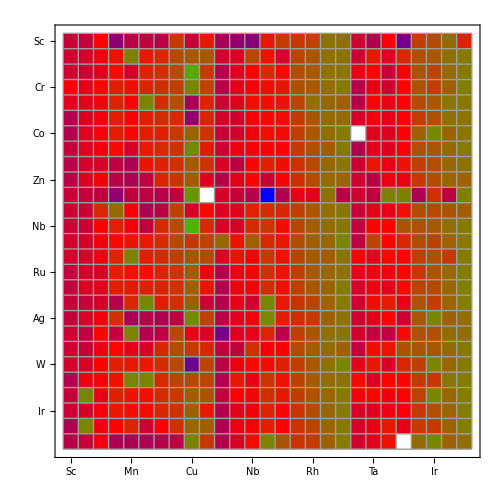

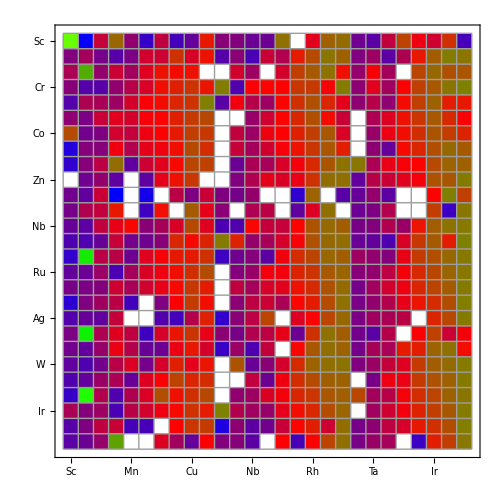

```mathematica
MatrixPlot[smallBindingTable,ColorFunction->(Blend[{Blue,Red, Green, Yellow},#]&),ColorRules->{0->White},Mesh->True,Frame->True,FrameTicks->({#,#}&@Transpose@{Range@Length@elements,elements}),PlotRangePadding->None,ImageSize->500]

MatrixPlot[bigBindingTable,ColorFunction->(Blend[{Blue,Red, Green, Yellow},#]&),ColorRules->{0->White},Mesh->True,Frame->True,FrameTicks->({#,#}&@Transpose@{Range@Length@elements,elements}),PlotRangePadding->None,ImageSize->500]
```

## Make Bar Charts:

### These statements are used to filter out spurious binding energies. Then nanoparticle removed has its corresponding label removed, so that the bar chart bars and their labes line up correctly

{{12}}

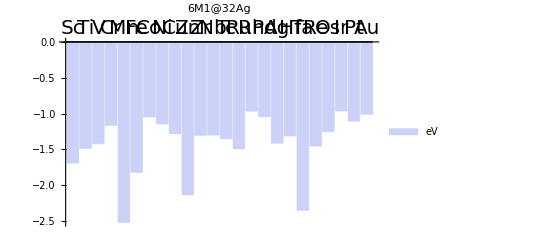

{{Sc},{Ti},{V},{Cr},{Mn},{Fe},{Co},{Ni},{Cu},{Zn},{Y},{Zr},{Nb},{Mo},{Tc},{Ru},{Rh},{Pd},{Ag},{Hf},{Ta},{W},{Re},{Os},{Ir},{Pt},{Au}}

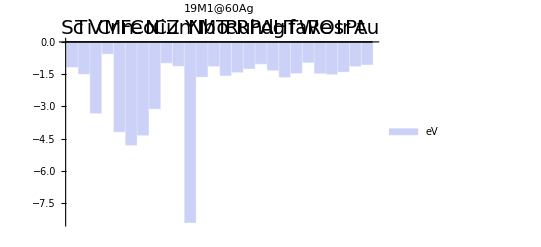

{{Sc},{Ti},{V},{Cr},{Mn},{Fe},{Co},{Ni},{Cu},{Zn},{Y},{Zr},{Nb},{Mo},{Tc},{Ru},{Rh},{Pd},{Ag},{Hf},{Ta},{W},{Re},{Os},{Ir},{Pt},{Au}}

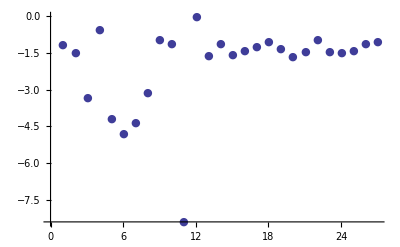

-Graphics-

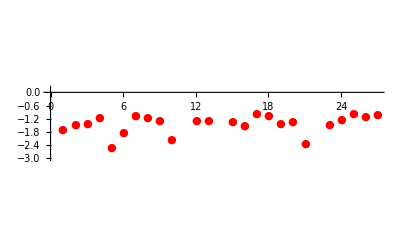

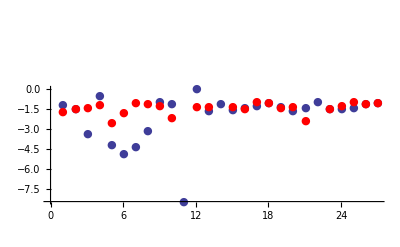

{0.528839,0.00008181,-1.8915,0.6229,-1.66226,-2.97975,-3.29121,-1.96083,0.313333,1.02347,1.6646,1.30394,-0.314616,-5.48928,-0.205317,0.0908144,-0.267932,0.0252885,0.100085,-0.317968,0.904503,-5.36616,0.00134848,-0.242626,-0.417037,-0.0155537,-0.0349103}

```mathematica
placeholder =DeleteCases[Map[ If[# >0 || # <-10 ,0,#] &,smallBindingTable[[All,19]] ],0];
removedElementsPos = Position[Map[ If[# >0 || # <-10 ,0,#] &,smallBindingTable[[All,19]] ],0];
newElementsSmall = Delete[elements, # & /@removedElementsPos] ;

placeholder2 =DeleteCases[Map[ If[# >0 || # <-10 ,0,#] &,bigBindingTable[[All,19]] ],0];
removedElementsPos2 = Position[Map[ If[# >0 || # <-10,0,#] &,bigBindingTable[[All,19]] ],0]
newElementsBig = Delete[elements, # & /@removedElementsPos2] ;
newElementsSmall == newElementsBig;
Delete[placeholder2, 1] ;

BarChart[placeholder,ChartLabels->{Placed[Style[#,FontSize->20]&/@newElementsSmall,Above]},PlotLabel->Style["6M1@32Ag",Bold,50],ChartLegends->{"eV"}]
{#} & @@{#, Medium } & /@  elements

BarChart[placeholder2,ChartLabels->{Placed[Style[#,FontSize->20]&/@newElementsBig,Above]},PlotLabel->Style["19M1@60Ag",Bold,50],ChartLegends->{"eV"}]
{#} & @@{#, Medium } & /@  elements
p1 = ListPlot[{#} & @bigBindingTable[[All,19]], FillingStyle-> Thick, PlotMarkers -> {Automatic, Medium}]


Show[p1,Graphics[{Red,elements}] ]
p2 = ListPlot[smallBindingTable[[All,19]], FillingStyle-> Thick, PlotMarkers -> {Automatic, Medium}, PlotStyle -> Red]
Show[p1,p2]
bigBindingTable[[All, 19]] - smallBindingTable[[All,19]]
```

## Ag, Pt Dot Chart

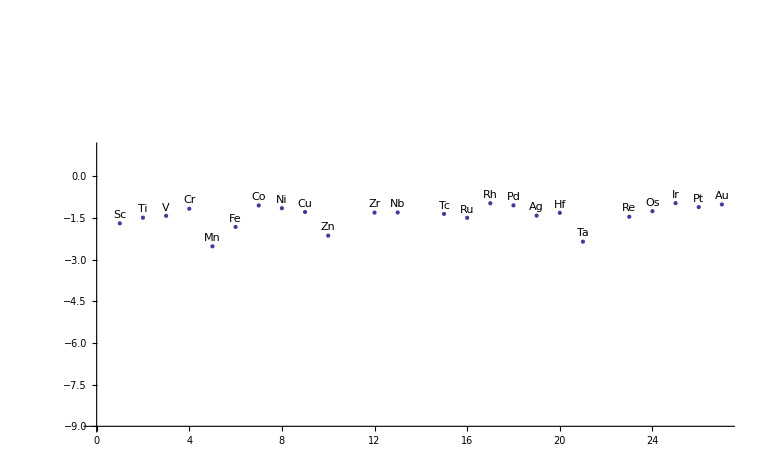

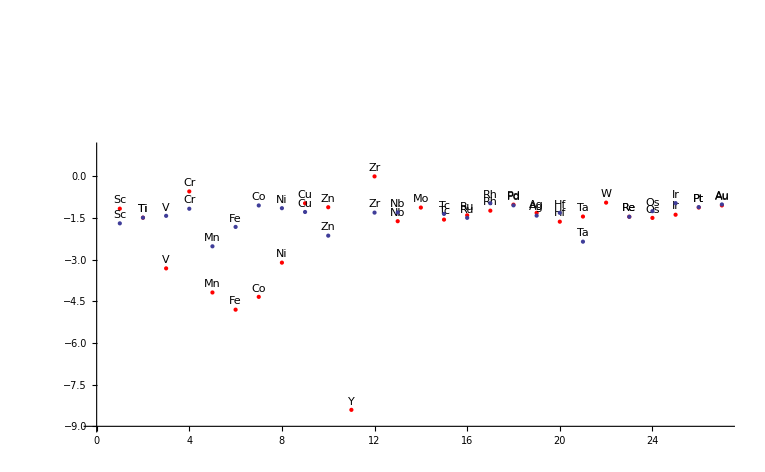

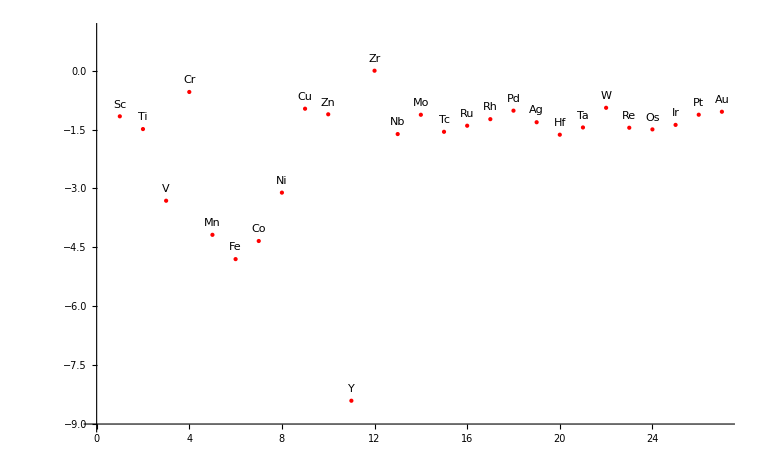

-Graphics-

```mathematica
dataPlot1=ListPlot[smallBindingTable[[All,19]],PlotStyle->PointSize->Large,AxesOrigin->{0,-9},PlotRange->{Automatic,{-9,1}}];
labels1=MapThread[Text[#1,{#2,#3+0.3}]&,{elements,Range[Length@smallBindingTable[[All,19]]],smallBindingTable[[All,19]]}];
Show[dataPlot1,Graphics[labels1]]

dataPlot2=ListPlot[bigBindingTable[[All,19]],PlotStyle->{Red,PointSize->Large},AxesOrigin->{0,-9},PlotRange->{Automatic,{-9,1}}];
labels2=MapThread[Text[#1,{#2,#3+0.3}]&,{elements,Range[Length@bigBindingTable[[All,19]]],bigBindingTable[[All,19]]}];

Show[dataPlot2,Graphics[labels2], dataPlot1, Graphics[labels1]]
Show[dataPlot2,Graphics[labels2]]
Show[dataPlot1, Graphics[labels1]]
```

```mathematica
lst = Delete[lst,3]
```

Delete::partw: Part {3} of lst does not exist.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

Delete::partw: Part {3} of Delete[Delete[Hold[Delete[lst, 3]], 3], 3] does not exist.

Delete::partw: Part {3} of Delete[Delete[Delete[Hold[Delete[lst, 3]], 3], 3], 3] does not exist.

Delete::partw: Part {3} of Delete[Delete[Delete[Delete[Hold[Delete[lst, 3]], 3], 3], 3], 3] does not exist.

General::stop: Further output of Delete :: partw will be suppressed during this calculation.

Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[MaxFormatDepthExceededMaxFormatDepthExceededMaxFormatDepthExceeded],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3]

## Average Bond Length Plots:

```mathematica
bondLenData = Import["/home/marco/fridbDemo/avgbondlen.json"] /. elementList;
```

Get Bond Length for bnp 38 nanoparticles

```mathematica
lst=  "bnp" /. bondLenData[[1]];
lst = "38" /. lst;

lst = Delete[lst,3];
lst = Delete[lst,8];
bnp38BL = Table[x, {x,1,27}] /. lst;
```

Get Bond Length for bnp 79 nanoparticles:

```mathematica
lst2=  "bnp" /. bondLenData[[1]];
lst2 = "79" /. lst2;
lst2 = Delete[lst,3];
lst2 = Delete[lst,8];
bnp79BL = Table[x, {x,1,27}] /. lst2; 

bondLenData[[1]]
```

bnp→{38→{19→2.85077,27→2.8549,Cd→2.88438,7→2.8297,4→2.84034,9→2.81286,6→2.8282,20→2.96446,Hg→2.87532,25→2.83727,5→2.83799,14→2.84114,13→2.91995,8→2.83038,24→2.84655,18→2.84554,26→2.84533,23→2.86048,17→2.84004,16→2.84042,1→2.92212,21→2.91318,15→2.85081,2→2.88824,3→2.87623,22→2.89723,11→2.96313,10→2.84196,12→2.97649},79→{19→2.87259,27→2.87463,Cd→2.88172,7→2.78466,4→2.82841,9→2.80938,6→2.77798,20→3.00874,25→2.81191,5→2.80125,14→2.82716,13→2.83941,8→2.7879,24→2.79815,18→2.82765,26→2.83002,23→2.8378,17→2.81816,16→2.80325,1→2.9742,21→2.96703,15→2.82528,2→2.8858,3→2.80727,22→2.83959,11→2.96012,10→2.85065}}

Make Plots of Bond Length data:

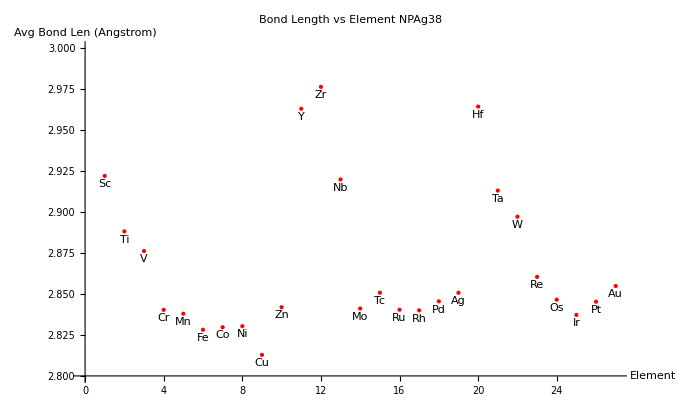

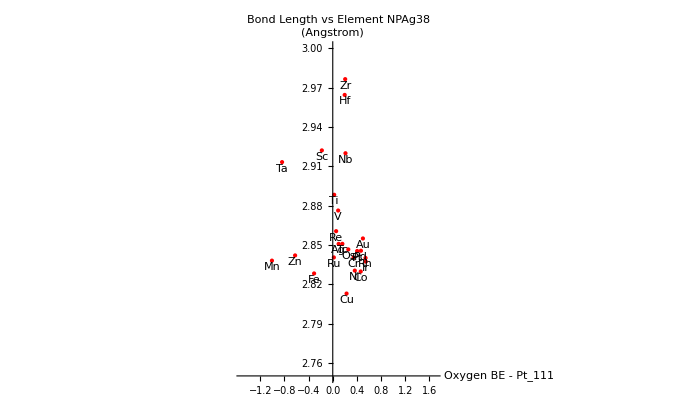

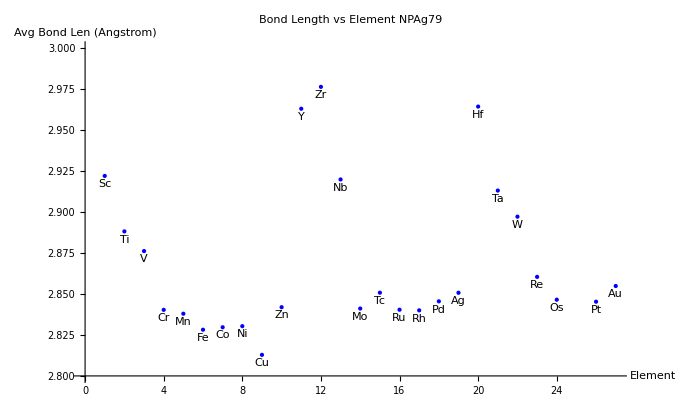

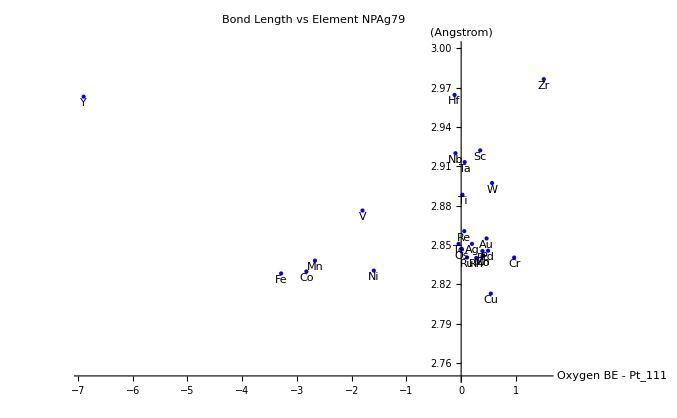

```mathematica
bondLenVsElement38 = ListPlot[bnp38BL, PlotStyle -> {Red, PointSize -> Large},PlotRange -> {2.80, 3},  PlotLabel -> "Bond Length vs Element NPAg38", AxesLabel->{"Element", "Avg Bond Len (Angstrom)"}];
bondLenVsElementLabels38=MapThread[Text[#1,{#2,#3-0.005}]&,{elements,Range[Length@bnp38BL], bnp38BL}];

bondLenVsBe38data = Partition[#,2] & @Riffle[#1, #2] & @@{smallBindingTable[[All,19]] - ORR /. targets, bnp38BL};
bondLenVsBe38=ListPlot[bondLenVsBe38data, PlotStyle->{Red,PointSize->Large}, PlotRange->{2.75, 3}, PlotLabel -> "Bond Length vs Element NPAg38", AxesLabel->{"Oxygen BE - Pt_111", "(Angstrom)"}];
bondLenVsBeLabels38=MapThread[Text[#1,{#2 ,#3- 0.005}]&,{elements,smallBindingTable[[All,19]] - ORR /. targets, bnp38BL}];

bondLenVsElement79 = ListPlot[bnp79BL, PlotStyle -> {Blue, PointSize -> Large},PlotRange -> {2.80, 3},  PlotLabel -> "Bond Length vs Element NPAg79", AxesLabel->{"Element", "Avg Bond Len (Angstrom)"}];
bondLenVsElementLabels79=MapThread[Text[#1,{#2,#3-0.005}]&,{elements,Range[Length@bnp79BL], bnp79BL}];

bondLenVsBe79data = Partition[#,2] & @Riffle[#1, #2] & @@{bigBindingTable[[All,19]] - ORR /. targets, bnp79BL};
bondLenVsBe79=ListPlot[bondLenVsBe79data, PlotStyle->{Blue,PointSize->Large}, PlotRange->{2.75, 3}, PlotLabel -> "Bond Length vs Element NPAg79", AxesLabel->{"Oxygen BE - Pt_111", "(Angstrom)"}];
bondLenVsBeLabels79=MapThread[Text[#1,{#2 ,#3- 0.005}]&,{elements,bigBindingTable[[All,19]] - ORR /. targets, bnp79BL}];




Show[bondLenVsElement38, Graphics[bondLenVsElementLabels38] ]
Show[bondLenVsBe38, Graphics[bondLenVsBeLabels38] ]

Show[bondLenVsElement79, Graphics[bondLenVsElementLabels79] ]
Show[bondLenVsBe79, Graphics[bondLenVsBeLabels79] ]
```

## Filter Particles:

```mathematica
idealORRSmall = Replace[smallBindingTable- (ORR) /. targets,a_/;Abs[a]≥0.05->0,{2}] ;
idealORRBig = Replace[bigBindingTable- (ORR) /. targets ,a_/;Abs[a] ≥0.05->0,{2}];
```

```mathematica
info[tbl_]:=With[{s=SparseArray[tbl]},ArrayPad[Append@@@Transpose[{s["NonzeroPositions"],s["NonzeroValues"]}],{0,{1,0}},ToString@Unevaluated@tbl]]

SetAttributes[info,HoldFirst]
MapAt[info,Replace[bigBindingTable- (ORR) /. targets ,a_/;Abs[a] ≥0.05->0,{2}],3]

info[idealORRSmall]/.  Reverse /@ elementList;
info[idealORRBig] /.  Reverse /@ elementList;
```

ArrayPad::depth: Padding amount {0, {1, 0}} should specify padding in no more than the number of dimensions in array {}.

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-0.00103932,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.0235657,0,0,0,0,0,0,0,0},ArrayPad[{},{0,{1,0}},{0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}],{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.0309183,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.0284615},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-0.046035,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-0.0441911,0,0,0,0,0,0,0,0.0172549,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.015038,0,0,0,0,0,0,0.0314884,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

### Filter For Tunable Particles:

```mathematica
returnValue[row_, col_,tbl_] := tbl[[row,col]] 

(* get diagonal elements.  A particle is tunable if its pure form is on the opposite side of the volcano from its core@shell partner.  Assume The list we are operating on has had the target binding energy subtracted from every entry in the table.  Then two particles are on opposite sides of the volcano if one has a positive energy and the other has a negative energy.  Here we search the diagnol (which corresponds to a pure particle). At each diagonal step we search the column.  If any element in the column is opposite in sign from any core elements (the column) then the particle is tunable.*)

filterTunable[tbls_, rxnTarget_]:= Function[myTable,{
f1 = Replace[myTable,a_/;Abs[a]≥ 0->0,{2}];
f1 = DeleteCases[f1,{__,0}]
tunableORRData=f1- rxnTarget/.targets; (*set any spurious values to zero *)
(* A particle is tunable if its pure form (located on the diagnols of the table) is opposite in sign to its core@shell parnter *)
d=Sign@Diagonal@tunableORRData;

tunablePairs=Position[(tunableORRDataᵀ d)ᵀ,_?Negative]/.Reverse/@elementList;
pairEnergy=returnValue[#1,#2, myTable]&@@{#1,#2}&@@@Position[(tunableORRDataᵀ d)ᵀ,_?Negative];
tempVar=Partition[Riffle[tunablePairs,pairEnergy],2];
filterImposs=Replace[tempVar,a_/;Abs[a]≥5->0,{2}];
filterImposs=Replace[filterImposs,a_/;a>1->0,{2}];
Cases[filterImposs,{x_,y_}/;y≠0]}][#, rxnTarget]&/@tbls ;

preProcTunable[tbls_, bintbl_]:= Function[myTable,{
tst =  bintbl[[#,#]] & /@ Flatten[myTable[[1,All,1,2]]  /. elementList];
 MapThread[Append,{myTable[[1]],tst}]}][#] & /@ tbls


idealRatio[EbCoreShell_ ,EbPt111_,EbPure_]:= (EbCoreShell - EbPt111)/(EbCoreShell - EbPure) 


filterTunable[{smallBindingTable}, ORR]
```

Set::write: Tag Times in tunableORRData\ {} is Protected.

Diagonal::list: List expected at position 1 in Diagonal[tunableORRData].

{{{}}}

```mathematica
Position[posData[[All,2]], 19]
posData[[18]]
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

{}

Part::partd: Part specification posData ⟦ 18 ⟧ is longer than depth of object.

posData⟦18⟧

```mathematica
Histogram[%4589]
```

Histogram::ldata: %4589 is not a valid dataset or list of datasets.

Histogram[%4589]

```mathematica
|
```

### Filter ORR Small Tunable:

```mathematica
tst =  smallBindingTable[[#,#]] & /@ Flatten[tunableSmall[[1,All,1,2]] /. elementList];
small = MapThread[Append,{tunableSmall[[1]],tst}];
ratioList = idealRatio[small[[All, 2]], -1.51, small[[All,3]]];
impossFilter1 = Replace[ratioList,a_/;Abs[a]≥1->"no",{1}];
impossFilter2 = Replace[impossFilter1,a_/;a <0->"no",{1}];
combineFilter = ArrayFlatten[{{small,Transpose[{impossFilter2}]}}];

finalSmallTunable = DeleteCases[combineFilter,{__,"no"}];
```

Part::partd: Part specification tunableSmall ⟦ 1, All, 1, 2 ⟧ is longer than depth of object.

Part::pspec: Part specification tunableSmall is neither a machine-sized integer nor a list of machine-sized integers.

Part::pspec: Part specification -6.732 is neither a machine-sized integer nor a list of machine-sized integers.

Part::partd: Part specification tunableSmall ⟦ 1 ⟧ is longer than depth of object.

MapThread::mptd: Object tunableSmall ⟦ 1 ⟧ at position {2, 1} in MapThread[Append, {tunableSmall ⟦ 1 ⟧, « 1 » ⟦ -6.732, {{-6.732, -7.27517, -5.01151, -105.511, -9.4589, -7.59326, -9.36046, -3.41948, -6.79604, -4.47385, -28.8383, -87.6257, -123.857, -4.54772, -3.34368, -3.56681, -3.24293, -1.47187, -1.69071, -6.51991, -12.991, -5.28916, -180.394, -3.30855, -3.1094, -1.8083, -4.2198}, « 25 », {-10.3259, -6.82941, « 24 », -1.69444}}, -« 11 », -6.3862 ⟧}] has only 0 of required 1 dimensions.

Part::partd: Part specification MapThread[Append, {tunableSmall ⟦ 1 ⟧, {{-6.732, -7.27517, -5.01151, -105.511, -9.4589, -7.59326, -9.36046, -3.41948, -6.79604, -4.47385, -28.8383, -87.6257, -123.857, -4.54772, -3.34368, -3.56681, -3.24293, -1.47187, -1.69071, -6.51991, -12.991, -5.28916, -180.394, -3.30855, -3.1094, -1.8083, -4.2198}, « 25 », {-10.3259, -6.82941, -5.48113, « 22 », -2.31682, -1.69444}} ⟦ « 1 » ⟧ ⟦ « 1 » ⟧}] ⟦ « 1 » ⟧ is longer than depth of object.

Transpose::nmtx: The first two levels of the one-dimensional list {1.51  + MapThread[Append, {tunableSmall ⟦ 1 ⟧, Part[« 3 »] ⟦ -6.732, {« 27 »}, -6.732, -6.3862 ⟧}] ⟦ All, 2 ⟧/MapThread[Append, {Part[« 2 »], Part[« 5 »]}] ⟦ All, 2 ⟧ - MapThread[Append, {« 2 »}] ⟦ All, 3 ⟧} cannot be transposed.

### Filter ORR Large Tunable:

```mathematica
tst = bigBindingTable[[#,#]] & /@ Flatten[tunableBig[[1,All,1,2]] /. elementList];
big = MapThread[Append,{tunableBig[[1]],tst}];
ratioList = idealRatio[big[[All, 2]], -1.51, big[[All,3]]];
impossFilter1 = Replace[ratioList,a_/;Abs[a]≥1->"no",{1}];
impossFilter2 = Replace[impossFilter1,a_/;a <0->"no",{1}];
combineFilter = ArrayFlatten[{{big,Transpose[{impossFilter2}]}}];

finalBigTunable = DeleteCases[combineFilter,{__,"no"}];

tunableBig

(*finalBigTunable/.{{l1_,l2_},x1_,x2_,_}:>MapThread[Labeled[{l2/.elementList,#},#2]&,{{x1,x2},{l1,l2}}]*)
```

Part::partd: Part specification tunableBig ⟦ 1, All, 1, 2 ⟧ is longer than depth of object.

Part::pspec: Part specification tunableBig is neither a machine-sized integer nor a list of machine-sized integers.

Part::pspec: Part specification 156.593 is neither a machine-sized integer nor a list of machine-sized integers.

Part::partd: Part specification tunableBig ⟦ 1 ⟧ is longer than depth of object.

MapThread::mptd: Object tunableBig ⟦ 1 ⟧ at position {2, 1} in MapThread[Append, {tunableBig ⟦ 1 ⟧, « 1 » ⟦ 156.593, {{156.593, -52.0823, -4.8808, -1.38635, -5.99529, -20.0851, -5.10796, -13.6342, -7.31414, -3.21067, -6.26199, -6.32499, -6.99733, -6.96793, -1.04173, 0, -4.19145, -1.51104, -1.16187, -6.84807, -8.31656, -5.06085, -2.33724, -4.02743, -4.54608, -2.71657, -13.4038}, « 25 », {-8.11528, -6.96224, -5.8536, « 21 », -3.11806, -2.45439, -0.786697}}, « 11 », -5.59122 ⟧}] has only 0 of required 1 dimensions.

Part::partd: Part specification MapThread[Append, {tunableBig ⟦ 1 ⟧, « 1 »}] ⟦ All, 2 ⟧ is longer than depth of object.

Part::partd: Part specification MapThread[Append, {tunableBig ⟦ 1 ⟧, « 1 »}] ⟦ All, 3 ⟧ is longer than depth of object.

Transpose::nmtx: The first two levels of the one-dimensional list {1.51  + MapThread[Append, {tunableBig ⟦ 1 ⟧, Part[« 3 »] ⟦ 156.593, {« 27 »}, 156.593, -5.59122 ⟧}] ⟦ All, 2 ⟧/MapThread[Append, {Part[« 2 »], Part[« 5 »]}] ⟦ All, 2 ⟧ - MapThread[Append, {« 2 »}] ⟦ All, 3 ⟧} cannot be transposed.

tunableBig

## Final Figures:

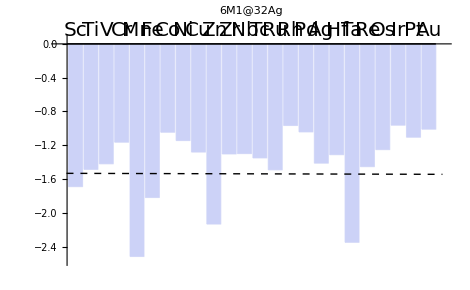
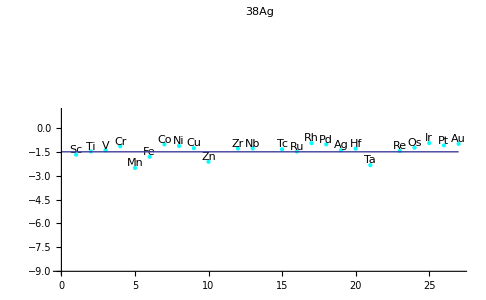
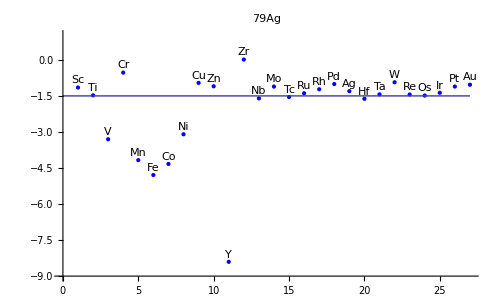
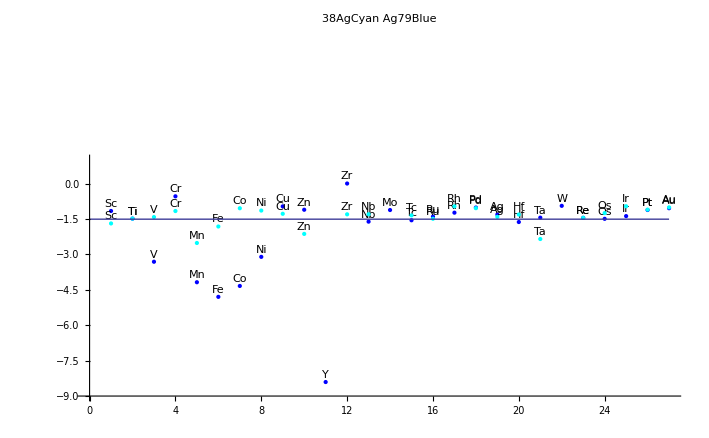
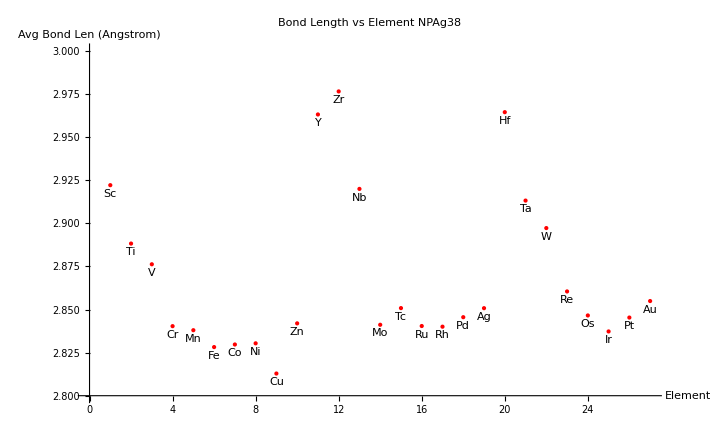
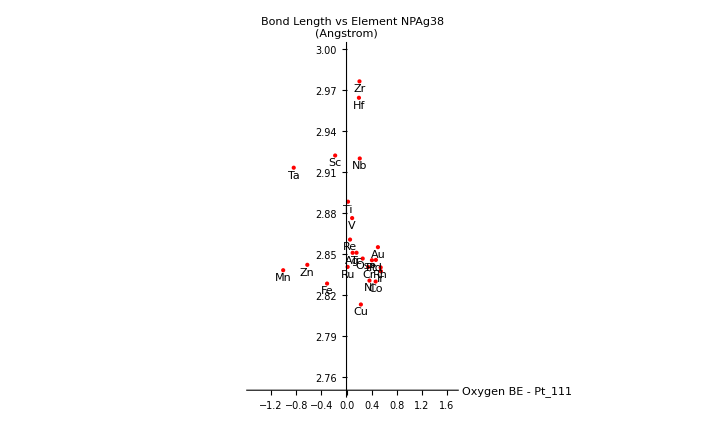
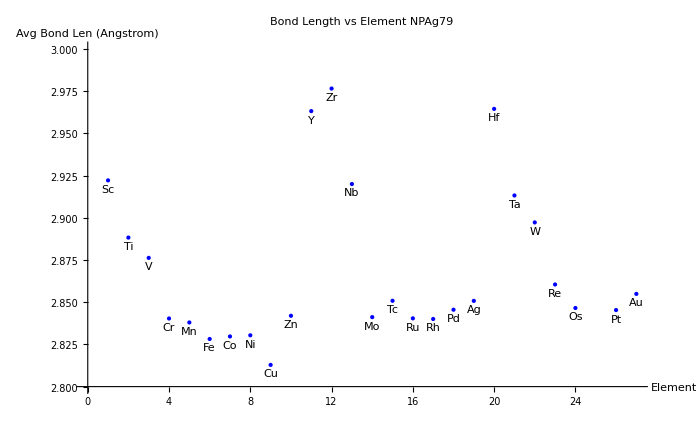
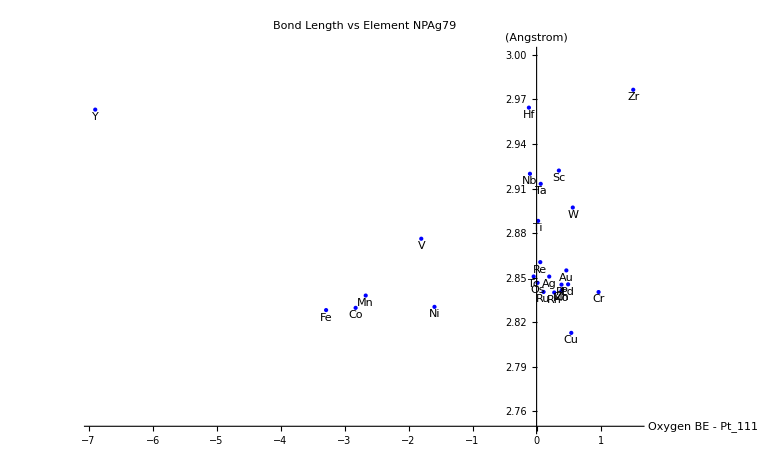
```mathematica
Figures I want to keep:
-Graphics-
-Graphics--Graphics-
-Graphics-

-Graphics--Graphics-

-Graphics--Graphics-

-Graphics--Graphics-

-Graphics-
```

Figures I want to keep:
-Graphics-
-Graphics--Graphics-
-Graphics-

-Graphics--Graphics-

-Graphics--Graphics-

-Graphics--Graphics-

-Graphics-

```mathematica
Figures I want to keep:
-Graphics-
-Graphics--Graphics-
-Graphics-

-Graphics--Graphics-

-Graphics-
```

Figures I want to keep:
-Graphics-
-Graphics--Graphics-
-Graphics-

-Graphics--Graphics-

-Graphics-

```mathematica
stackTest = {{1,2,3,4,5,6,7,8,9,10}}
```

{{1,2,3,4,5,6,7,8,9,10}}

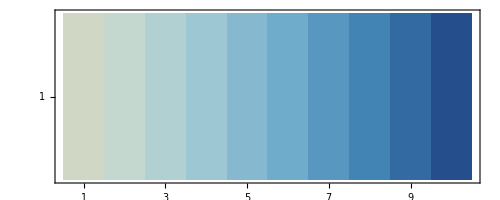

```mathematica
MatrixPlot[stackTest, ColorFunction->"RedBlueTones"]
```

```mathematica
Length[tunableORRData]
```

0

```mathematica
smallBindingTable
```

{{-6.732,-7.27517,-5.01151,-105.511,-9.4589,-7.59326,-9.36046,-3.41948,-6.79604,-4.47385,-28.8383,-87.6257,-123.857,-4.54772,-3.34368,-3.56681,-3.24293,-1.47187,-1.69071,-6.51991,-12.991,-5.28916,-180.394,-3.30855,-3.1094,-1.8083,-4.2198},{-6.57407,-6.3862,-5.45389,-4.65331,0.860106,-4.46683,-4.01216,-3.1242,-2.74773,-2.80093,-6.39748,-6.09923,-3.18594,-4.5779,-6.36042,-3.23825,-2.92423,-1.61127,-1.48652,-6.57345,-4.54179,-6.08298,-3.93447,-3.02605,-2.86587,-1.63843,-1.19295},{-6.54497,-6.53329,-6.0358,-4.78015,-6.37304,-4.20426,-3.80912,-3.1112,107.983,-3.46504,-11.9687,-6.03031,-5.06045,-3.96864,-4.90052,-3.07008,-2.81276,-1.60509,-1.42055,-5.76192,-5.01714,-6.96436,-5.20379,-2.96113,-3.26455,-1.87771,-1.10513},{-5.28476,-5.87817,-4.8642,-4.36083,-4.75426,-4.13973,-3.82682,-3.33217,4.34293,-3.2243,-9.61628,-5.80414,-5.41101,-4.79706,-4.55506,-3.06878,-2.69414,-1.7745,-1.16451,-10.9609,-5.70199,-6.50406,-5.03668,-2.9779,-3.33661,-2.29656,-0.131714},{-6.02304,-5.82231,-5.32531,-4.2108,-4.97377,3.10849,-3.88977,-3.03449,-30.2487,-4.1564,-6.57849,-5.88691,-4.79628,-4.70149,-4.63215,-3.24935,-1.55186,-1.90981,-2.51796,-9.72864,-5.1199,-5.64631,-5.04048,-3.07473,-2.71754,-1.29537,-1.21843},{-13.0879,-6.05419,-5.44884,-4.33451,-5.13699,-4.33105,-3.918,-3.95997,-84.9591,-4.12367,-6.33317,-6.38844,-5.32993,-4.90242,-4.78625,-3.41748,-2.88007,-1.79372,-1.81939,-6.33952,-5.42191,-5.80547,-5.06802,-3.41229,-2.99085,-1.54796,-1.44088},{-13.0006,-5.96781,-5.2165,-4.37512,-4.97284,-4.33114,-4.33615,-3.53216,-2.26743,-3.61848,-6.66744,-6.41409,-5.52062,-4.73777,-4.78966,-3.39506,-2.94096,-1.8705,-1.04659,0,-5.9382,-6.07371,-5.12424,-2.35279,5.22045,-2.23698,-1.30395},{-6.9298,-5.99329,-5.39335,-4.821,-6.24834,-4.45547,-3.98886,-3.58221,4.422,-4.38025,-6.57842,-5.59534,-5.20524,-5.14707,-5.0522,-3.47045,-3.00545,-2.5603,-1.14478,-12.637,-5.87252,-6.0438,-5.16825,-3.04447,-2.85679,-2.00655,-0.671956},{-10.1741,-6.27368,-6.19217,-8.31004,-17.3761,-4.63675,-4.22869,-3.66886,-2.55195,-3.60933,-6.14067,-7.95486,-4.96954,-4.30542,-4.72473,-3.64541,-3.12462,-2.05841,-1.2814,-6.63924,-4.56169,-5.68116,-4.60079,-3.29129,-3.06652,-2.07835,-1.51495},{-9.78975,-6.09903,-5.35288,-9.62582,-15.1995,-7.54962,-4.20816,-3.57802,-2.73171,-6.00803,-10.1792,-5.90802,-5.13033,-6.74419,-5.22573,-3.81919,-3.15717,-1.87809,-2.13397,-6.53378,-9.22608,-5.67645,-5.67967,-3.55864,-3.11476,-2.08233,-2.16209},{-6.8173,-7.14565,-7.95136,-90.5081,-7.72887,-8.45685,-10.5746,-7.59255,44.8605,0,-6.36134,-6.67835,-10.641,-541.025,-14.6376,-5.72627,-5.96966,-1.56194,-10.0711,-6.48629,-7.5176,-0.189288,1.19153,-19.0715,-3.75936,-7.98813,1.2205},{-6.63861,-6.65831,-3.98049,-1.90822,-5.1863,-16.6328,-8.84615,-3.28998,-6.2878,-4.81045,-6.10997,-5.89325,-4.2119,-3.89886,-4.14224,-3.41,-2.8825,-1.60735,-1.30394,-6.72428,-5.83372,-5.79673,-4.66692,-3.10247,-3.1188,-2.96714,-2.46874},{-6.62186,-6.6907,-5.11316,-4.22,-5.37438,-7.53593,-3.90362,-3.10452,136.641,-3.93171,-6.11813,-6.13659,-3.82354,-3.57326,-4.76024,-3.19129,-2.54989,-1.65592,-1.29924,-7.26422,-5.02008,-5.10755,-2.962,-3.00746,-2.75403,-1.77984,-1.087},{-6.48357,-6.36289,-5.46906,-4.84749,-4.55823,-4.44518,-3.91444,-3.17035,-3.58145,-3.30349,-1.99753,-4.60329,-2.44094,-3.94854,-4.54097,-3.07597,-2.55175,-1.92627,4.36713,-8.24918,-3.24031,-5.0098,-3.99774,-3.10698,-3.27815,-2.17434,-1.1764},{-6.46705,-6.3184,-5.59829,-4.1004,2.55369,-4.36603,-3.99099,-3.33538,-2.95589,-3.15032,-6.07776,-4.66455,-5.40433,-3.523,-4.5672,-3.28042,-2.68259,-2.46921,-1.35072,-5.1584,-5.81326,-4.88849,-4.88852,-3.39901,-3.00302,-3.48518,-0.922638},{-7.19689,-6.286,-6.16488,-4.23323,-4.55508,-4.6794,-4.16524,-3.60022,-2.64165,-5.50071,-11.8133,-5.63919,-5.16434,-3.73418,-4.55187,-3.34079,-2.7642,-2.04738,-1.49208,-5.78859,-5.51309,-5.43795,-4.92475,-3.57668,-2.95432,-2.03626,-0.787955},{-7.56776,-6.07736,-5.97566,-4.33796,-4.50586,-4.3043,-4.14986,-3.63601,-2.35353,-4.57655,-12.296,-5.62819,-5.39405,-3.83913,-4.68654,-3.29405,-2.83568,-2.13715,-0.966458,-6.29401,-5.50667,-5.94071,-4.85884,-3.22235,-3.1394,-2.07589,-0.482705},{-6.92467,-6.72004,-6.32581,-11.0014,-4.13434,4.43605,-4.37728,-3.73436,-2.41587,-6.62543,-12.0309,-5.7205,-6.39687,4.42889,-4.40312,-3.64166,-3.25703,-2.21809,-1.0429,-6.48135,-4.83744,-4.41985,-5.70304,-2.99609,-3.3895,-2.15726,-0.379127},{-6.84269,-6.26751,-5.42024,-3.71058,-19.9224,-10.6631,-14.2833,-8.85643,13.5035,-3.30866,-8.86033,-5.89122,-5.36625,6.03698,-4.29201,-3.84606,-3.41949,-2.23744,-1.41273,-6.48503,-5.86511,-5.06686,-6.57937,-2.8647,4.42182,-2.25204,-1.72996},{-6.61541,-7.55283,-4.92089,-6.99641,2.55403,-12.3982,-8.18252,-3.22926,-5.60863,-6.0927,-176.772,-6.06518,-5.80175,-4.04486,-9.05536,-3.31957,-2.81817,-1.62158,-1.31235,-6.42587,-7.46793,-7.5369,-4.86036,-3.00894,-3.05479,-1.63904,-1.63271},{-6.5904,-6.74637,-5.65934,-4.92189,-5.74707,-6.24705,-3.99528,-3.10146,-3.50936,-4.04648,-7.10375,-7.05281,-3.66082,-5.21088,-5.15964,-3.15559,-2.55747,-1.66047,-2.3501,-7.22216,-4.75924,-4.57433,-3.00234,-2.95792,-2.83783,-1.80795,-1.12029},{-6.42686,-6.21165,-5.05349,-4.29623,-4.54741,-4.46051,-3.86132,-3.16422,-197.533,-3.26868,-8.31362,-5.52697,-4.84873,-4.76133,-4.24107,-3.33038,-2.7658,-1.52766,4.42157,-5.87914,-4.5517,-6.11537,-4.05227,-3.36523,4.42193,-2.01085,-1.16135},{-12.4213,-5.65464,-5.17227,-4.68497,2.85118,2.20532,-3.96304,-3.20929,-3.13041,-3.20482,-13.1203,-4.54927,-5.74259,-3.5778,-4.61148,-3.31737,-2.68263,-1.85017,-1.45391,-4.80219,-6.08356,-4.97745,-4.88537,-3.41598,-3.52136,-1.22974,-1.04512},{-7.07662,4.23474,-5.80317,-4.26711,-4.55521,-4.67878,-3.9448,-3.53662,-2.64505,-2.97908,-7.04467,-5.08131,-5.15957,-3.85669,-4.54198,-3.45615,-2.96828,-2.01866,-1.25234,-5.48023,-4.93588,-5.48682,-5.1458,-3.31349,4.60888,-2.06396,-0.76104},{-6.61833,-6.36406,-5.35434,-4.53383,-4.70117,-4.74689,-4.03604,-3.59924,-2.31568,-4.46419,-12.1633,-5.88673,-5.45283,-4.14308,-4.92745,-3.59097,-3.08165,-2.10359,-0.963033,-6.26121,-6.0361,-5.51066,-5.25085,-3.47908,-3.06277,-2.09982,-0.578992},{-14.1286,4.42145,-5.43098,-4.9017,-4.17768,-6.60889,-5.15888,-3.6883,-2.07893,-2.38308,-13.1342,-5.63728,-5.19096,-4.33398,-5.11143,-3.63746,-3.24358,-2.14413,-1.10553,-6.2898,-5.69808,-4.53879,-5.70431,-3.4492,-3.46141,-2.25102,-0.593863},{-10.3259,-6.82941,-5.48113,-15.0043,-18.5632,-16.3959,-9.51913,-9.05336,1.15258,-3.50652,-12.1426,-6.15909,-4.79829,3.73948,-2.97537,-3.79717,-3.46909,-2.26438,-1.01026,-6.484,-5.94237,-4.68558,0,-1.87671,4.42182,-2.31682,-1.69444}}

```mathematica
Function[myTable, {tunableORRData = Replace[myTable ,a_/;Abs[a]≥10->0,{2}] - ORR /. targets;d=Sign@Diagonal@tunableORRData; returnValue[row_, col_,myTable] := myTable[[row,col]] ;tunablePairs = Position[(tunableORRDataᵀ d)ᵀ,_?Negative]  /. Reverse /@ elementList; pairEnergy = returnValue[#1, #2]& @@{#1,#2}&@@@Position[(tunableORRDataᵀ d)ᵀ,_?Negative] ;
tempVar = Partition[Riffle[tunablePairs, pairEnergy],2];
filterImposs = Replace[tempVar,a_/;Abs[a]≥5->0 ,{2}] ;
filterImposs = Replace[filterImposs,a_/;a > 1->0 ,{2}] ;
Cases[filterImposs,{x_,y_}/;y ≠ 0]}][#] & /@ {smallBindingTable, bigBindingTable}








(*Cases[tt,x_/;Abs[x[[1]]-x[[2]]]>3];*)
```

{{{}},{{}}}

```mathematica
{#,#}[[1]]&@Transpose@{Range@Length@elements, elements}
```

{{1,Sc},{2,Ti},{3,V},{4,Cr},{5,Mn},{6,Fe},{7,Co},{8,Ni},{9,Cu},{10,Zn},{11,Y},{12,Zr},{13,Nb},{14,Mo},{15,Tc},{16,Ru},{17,Rh},{18,Pd},{19,Ag},{20,Hf},{21,Ta},{22,W},{23,Re},{24,Os},{25,Ir},{26,Pt},{27,Au}}

```mathematica
f1 = Replace[myTable,a_/;Abs[a]≥ 0->"no",{2}];
f1 = DeleteCases[f1,{__,"no"}]
tunableORRData=f1- rxnTarget/.targets; (*set any spurious values to zero *)
(* A particle is tunable if its pure form (located on the diagnols of the table) is opposite in sign to its core@shell parnter *)
d=Sign@Diagonal@tunableORRData;

tunablePairs=Position[(tunableORRDataᵀ d)ᵀ,_?Negative]/.Reverse/@elementList;
pairEnergy=returnValue[#1,#2, myTable]&@@{#1,#2}&@@@Position[(tunableORRDataᵀ d)ᵀ,_?Negative];
tempVar=Partition[Riffle[tunablePairs,pairEnergy],2];
filterImposs=Replace[tempVar,a_/;Abs[a]≥5->0,{2}];
filterImposs=Replace[filterImposs,a_/;a>1->0,{2}];
Cases[filterImposs,{x_,y_}/;y≠0]}][#, rxnTarget]&/@tbls ;
```